```mathematica
Clear[x,y];
y[x_]=∫5ⅇ^(-3x)ⅆx+c
```

c-(5 ⅇ^(-3 x))/3

```mathematica
cval=Solve[y[0]==-10,c]
```

{{c→-25/3}}

```mathematica
c=cval[[1,1,2]]
```

-25/3

```mathematica
Factor[y[x]]
```

-5/3 ⅇ^(-3 x) (1+5 ⅇ^(3 x))

```mathematica
yprime[x_]=∫(ⅇ^(-2x)+1/x^2)ⅆx+c1
```

c1-ⅇ^(-2 x)/2-1/x

```mathematica
sol=Solve[yprime[1]==4,c1]
```

{{c1→(1+10 ⅇ^2)/(2 ⅇ^2)}}

```mathematica
c1=sol[[1,1,2]]
```

(1+10 ⅇ^2)/(2 ⅇ^2)

```mathematica
N[c1]
```

5.06767

```mathematica
c1
```

(1+10 ⅇ^2)/(2 ⅇ^2)

```mathematica
Clear[y];
y[x_]=∫yprime[x]ⅆx+c2
```

c2+1/2 (ⅇ^(-2 x)/2+10 x+x/ⅇ^2-2 Log[x])

```mathematica
sol=Solve[y[1]==2,c2]
```

{{c2→-(3 (1+4 ⅇ^2))/(4 ⅇ^2)}}

```mathematica
c2=sol[[1,1,2]]
```

-(3 (1+4 ⅇ^2))/(4 ⅇ^2)

```mathematica
y[x]
```

-(3 (1+4 ⅇ^2))/(4 ⅇ^2)+1/2 (ⅇ^(-2 x)/2+10 x+x/ⅇ^2-2 Log[x])

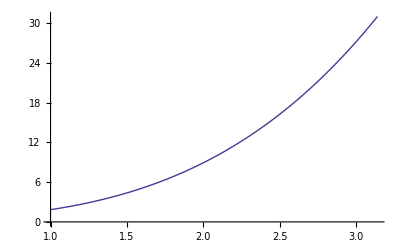

```mathematica
Clear[f,x,y];
f[x_]=x^3+Sin[x];
Plot[f[x],{x,1,π}]
```

```mathematica
dx=(π-1)/100;
fvals=Table[f[1+(i-.5)dx],{i,1,100}]
```

{1.87968,1.95789,2.03855,2.12171,2.20743,2.29575,2.38674,2.48045,2.57693,2.67624,2.77843,2.88356,2.99169,3.10286,3.21715,3.33459,3.45526,3.5792,3.70648,3.83715,3.97126,4.10888,4.25007,4.39487,4.54335,4.69558,4.85159,5.01147,5.17525,5.34301,5.5148,5.69069,5.87072,6.05497,6.24349,6.43635,6.63359,6.8353,7.04151,7.25231,7.46774,7.68787,7.91277,8.14249,8.37709,8.61665,8.86121,9.11085,9.36563,9.62561,9.89085,10.1614,10.4374,10.7188,11.0057,11.2983,11.5964,11.9003,12.21,12.5255,12.8469,13.1743,13.5077,13.8472,14.193,14.5449,14.9031,15.2678,15.6388,16.0164,16.4005,16.7912,17.1887,17.5929,18.004,18.422,18.8469,19.2789,19.718,20.1642,20.6177,21.0786,21.5467,22.0224,22.5055,22.9963,23.4947,24.0008,24.5147,25.0364,25.5661,26.1037,26.6495,27.2033,27.7654,28.3357,28.9143,29.5014,30.0969,30.701}

```mathematica
averageval=(Plus@@fvals)/100
```

11.9734

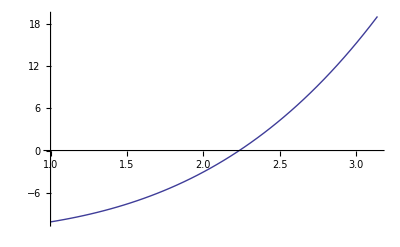

```mathematica
Plot[f[x]-averageval,{x,1,π}]
```

```mathematica
r=FindRoot[f[x]-averageval,{x,2.2,2.3}]
```

{x→2.23651}

```mathematica
NIntegrate[ⅇ^(-x^2),{x,-1,1}]
```

1.49365